```mathematica
(* shorten diagonmatrix *)
dm[m_]:=DiagonalMatrix[m];
(* spherical to carteisan coordinates - useful for parameterizing unit vectors *)
s2c[Φ_,Θ_]:={ Cos[Θ] Sin[Φ], Sin[Φ] Sin[Θ],Cos[Φ]};
```

```mathematica
(* Random Angle and Angle Vector *)
RA:=RandomReal[{0,2 Pi}];
```

```mathematica
h={{1,1},{1,-1}}/2;
```

```mathematica
M2=KroneckerProduct[h,h]
```

{{1/4,1/4,1/4,1/4},{1/4,-1/4,1/4,-1/4},{1/4,1/4,-1/4,-1/4},{1/4,-1/4,-1/4,1/4}}

```mathematica
({{1, 1, 1, 1}, {1, -1, 1, -1}, {1, 1, -1, -1}, {1, -1, -1, 1}})
```

```mathematica
M3=KroneckerProduct[h,h,h]
```

{{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8},{1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8},{1/8,1/8,-1/8,-1/8,1/8,1/8,-1/8,-1/8},{1/8,-1/8,-1/8,1/8,1/8,-1/8,-1/8,1/8},{1/8,1/8,1/8,1/8,-1/8,-1/8,-1/8,-1/8},{1/8,-1/8,1/8,-1/8,-1/8,1/8,-1/8,1/8},{1/8,1/8,-1/8,-1/8,-1/8,-1/8,1/8,1/8},{1/8,-1/8,-1/8,1/8,-1/8,1/8,1/8,-1/8}}

```mathematica
(*Now test the Hadamard Matrix Bell inequality I made*)
```

```mathematica
(* Full Symmetrization Triple Product *)
tripleSymProd[a_]:={a[[2]].a[[3]],a[[1]].a[[3]],a[[1]].a[[2]]}.a/3;
```

```mathematica
Qvalue2[A_,B_,Σ_]:=Total[Table[ A[[i]].Σ.B[[j]],{i,4},{j,4}]*M2,2];
```

```mathematica
Qvalue3[A_,B_,Σ_]:=Total[Table[ A[[i]].Σ.B[[j]],{i,8},{j,8}]*M3,2];
```

```mathematica
(* Use Mathematica Optimization*)
```

```mathematica
findQvalue2[a_,b_,Σ_]:=Module[{a012,b012,A,B},
a012=tripleSymProd[a];
A=Join[a,{a012}];

b012=tripleSymProd[b];
B=Join[b,{b012}];

Qvalue2[A,B,Σ]
]
```

```mathematica
(* ugly code, should be generalized to N *)
```

```mathematica
findQvalue3[a_,b_,Σ_]:=Module[{a012,a013,a023,a123,b012,b013,b023,b123,A,B},
a012=tripleSymProd[a[[{1,2,3}]]];
a013=tripleSymProd[a[[{1,2,4}]]];
a023=tripleSymProd[a[[{1,3,4}]]];
a123=tripleSymProd[a[[{2,3,4}]]];
A=Join[a[[{1,2,3}]],{a012},{a[[4]]},{a013},{a023},{a123}];

b012=tripleSymProd[b[[{1,2,3}]]];
b013=tripleSymProd[b[[{1,2,4}]]];
b023=tripleSymProd[b[[{1,3,4}]]];
b123=tripleSymProd[b[[{2,3,4}]]];
B=Join[b[[{1,2,3}]],{b012},{b[[4]]},{b013},{b023},{b123}];

Qvalue3[A,B,Σ]
]
```

```mathematica
getMax2[svalues_]:=Quiet[FindMaximum[findQvalue2[{s2c[Φa0,Θa0],s2c[Φa1,Θa1],s2c[Φa2,Θa2]},{s2c[Φb0,Θb0],s2c[Φb1,Θb1],s2c[Φb2,Θb2]},dm[svalues]],
{{Φa0,Pi/4},{Θa0,Pi/2},{Φa1,Pi/2},{Θa1,Pi},Φa2,Θa2,Φb0,Θb0,{Φb1,3 Pi/4},{Θb1,Pi/2},{Φb2,Pi/2},{Θb2,3Pi/2}},AccuracyGoal->9,PrecisionGoal->9, MaxIterations->3000]];
```

```mathematica
getvectors2[out_]:=Module[{a0,a1,a2,b0,b1,b2,mΦa0,mΘa0,mΦa1,mΘa1,mΦa2,mΘa2,mΦb0,mΘb0, mΦb1,mΘb1,mΦb2,mΘb2},
{mΦa0,mΘa0,mΦa1,mΘa1,mΦa2,mΘa2,mΦb0,mΘb0,mΦb1,mΘb1,mΦb2,mΘb2}={Φa0,Θa0,Φa1,Θa1,Φa2,Θa2,Φb0,Θb0,Φb1,Θb1,Φb2,Θb2}/.out[[2]];
{a0,a1,a2,b0, b1,b2}={s2c[mΦa0,mΘa0],s2c[mΦa1,mΘa1],s2c[mΦa2,mΘa2],s2c[mΦb0,mΘb0],s2c[mΦb1,mΘb1],s2c[mΦb2,mΘb2]};
(*output the vectors with their inner products *)
{{a0,a1,a2,tripleSymProd[{a0,a1,a2}]},{a1.a2,a0.a2,a0.a1},{b0,b1,b2,tripleSymProd[{b0,b1,b2}]},{b1.b2,b0.b2,b0.b1},{a0,a1,a2}.{b0,b1,b2}ᵀ}
]
```

```mathematica
getMax2[{1,1,0}]
```

{1.5,{Φa0→1.5708,Θa0→2.12692,Φa1→7.85398,Θa1→3.17412,Φa2→1.5708,Θa2→1.07973,Φb0→1.5708,Θb0→2.12692,Φb1→1.5708,Θb1→1.07973,Φb2→4.71239,Θb2→0.0325295}}

```mathematica
getvectors2[%]
```

{{{-0.527902,0.849305,-4.34623×10^-10},{-0.999471,-0.0325237,-7.23189×10^-10},{0.471569,0.881829,1.52944×10^-9},{4.56545×10^-10,-1.0249×10^-9,2.06812×10^-10}},{-0.5,0.5,0.5},{{-0.527902,0.849305,8.1363×10^-10},{0.471569,0.881829,-9.90175×10^-10},{-0.999471,-0.0325237,4.67038×10^-10},{2.03448×10^-10,3.77225×10^-10,-2.22794×10^-10}},{-0.5,0.5,0.5},{{1.,0.5,0.5},{0.5,-0.5,1.},{0.5,1.,-0.5}}}

```mathematica
(* so when I use Hadamard matrix instead of the one I had, I get same idea of dot product absolute values 0.5, but signs switch and a0=b0, a1=b2, a2=b1 (last two vectors switched)
```

```mathematica
getMax2[{1,.9,0}]
```

{1.4264,{Φa0→4.71239,Θa0→3.63309,Φa1→1.5708,Θa1→1.5708,Φa2→1.5708,Θa2→-0.491501,Φb0→1.5708,Θb0→0.491501,Φb1→4.71239,Θb1→2.65009,Φb2→4.71239,Θb2→4.71239}}

```mathematica
getvectors2[%]
```

{(-0.560619 | 0.828074 | 1.42653×10^-9
-0.997443 | -0.071473 | 4.77189×10^-9
0.436824 | 0.899547 | 4.06916×10^-10
6.14338×10^-10 | -1.53016×10^-9 | 6.2538×10^-10),{-0.5,0.5,0.5},(-0.560619 | 0.828074 | 1.9967×10^-9
0.436824 | 0.899547 | 1.23722×10^-9
-0.997443 | -0.071473 | -2.29378×10^-10
-1.44944×10^-9 | 2.26861×10^-9 | -1.64809×10^-10),{-0.5,0.5,0.5},(1. | 0.5 | 0.5
0.5 | -0.5 | 1.
0.5 | 1. | -0.5)}

```mathematica
(* this one is a close upper bound, but no dice ... but, may be it IS correct, it only becomes inaccurate at small values, where getmax is clearly in trouble anyways*)
try[x_,y_]:=N[√(x^2+x y /4 +y^2)];
```

```mathematica
try[1,.9]
```

1.42653

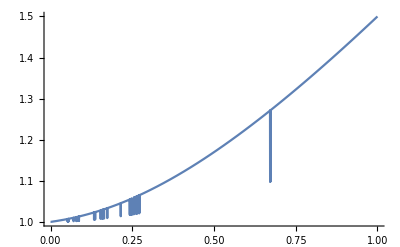

```mathematica
Plot[getMax2[{1,x,0}][[1]],{x,0,1}]
```

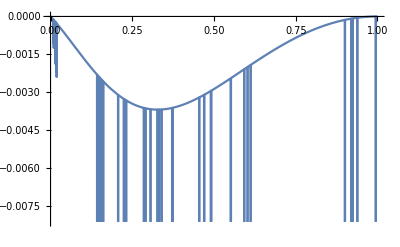

```mathematica
Plot[getMax2[{1,x,0}][[1]]-try[1,x],{x,0,1}]
```

```mathematica
(* so the "try" system above is good upper bound, fails in middle but very small, may be just machine error .. not sure though since does not decrease when I increase the machine accuracy and precision and iterations ... *)
```

```mathematica
getMax3[svalues_]:=Quiet[FindMaximum[findQvalue3[{s2c[Φa0,Θa0],s2c[Φa1,Θa1],s2c[Φa2,Θa2],s2c[Φa3,Θa3]},{s2c[Φb0,Θb0],s2c[Φb1,Θb1],s2c[Φb2,Θb2],s2c[Φb3,Θb3]},dm[svalues]],
{{Φa0,Pi/4},{Θa0,-Pi/2},{Φa1,Pi},{Θa1,2Pi/3},{Φa2,Pi/3},{Θa2,4Pi/3},{Φa3,3Pi/2},{Θa3,3Pi/4},Φb0,Θb0,{Φb1,3 Pi/4},{Θb1,Pi/2},{Φb2,Pi/2},{Θb2,3Pi/2},{Φb3,Pi},{Θb3,7Pi/8}},AccuracyGoal->9,PrecisionGoal->9, MaxIterations->3000]];
```

```mathematica
(* version with random starting points *)
getMax3r[svalues_]:=Quiet[FindMaximum[findQvalue3[{s2c[Φa0,Θa0],s2c[Φa1,Θa1],s2c[Φa2,Θa2],s2c[Φa3,Θa3]},{s2c[Φb0,Θb0],s2c[Φb1,Θb1],s2c[Φb2,Θb2],s2c[Φb3,Θb3]},dm[svalues]],
{{Φa0,RA},{Θa0,RA},{Φa1,RA},{Θa1,RA},{Φa2,RA},{Θa2,RA},{Φa3,RA},{Θa3,RA},{Φb0,RA},{Θb0,RA},{Φb1,RA},{Θb1,RA},{Φb2,RA},{Θb2,RA},{Φb3,RA},{Θb3,RA}},AccuracyGoal->9,PrecisionGoal->9, MaxIterations->10000]];
```

```mathematica
getvectors3[out_]:=Module[{a0,a1,a2,a3,b0,b1,b2,b3,mΦa0,mΘa0,mΦa1,mΘa1,mΦa2,mΘa2,mΦa3,mΘa3,mΦb0,mΘb0, mΦb1,mΘb1,mΦb2,mΘb2,mΦb3,mΘb3},
{mΦa0,mΘa0,mΦa1,mΘa1,mΦa2,mΘa2,mΦa3,mΘa3,mΦb0,mΘb0,mΦb1,mΘb1,mΦb2,mΘb2,mΦb3,mΘb3}={Φa0,Θa0,Φa1,Θa1,Φa2,Θa2,Φa3,Θa3,Φb0,Θb0,Φb1,Θb1,Φb2,Θb2,Φb3,Θb3}/.out[[2]];
{a0,a1,a2,a3,b0, b1,b2,b3}={s2c[mΦa0,mΘa0],s2c[mΦa1,mΘa1],s2c[mΦa2,mΘa2],s2c[mΦa3,mΘa3],s2c[mΦb0,mΘb0],s2c[mΦb1,mΘb1],s2c[mΦb2,mΘb2],s2c[mΦb3,mΘb3]};
(*output the vectors with their inner products *)
{{a0,a1,a2,a3,tripleSymProd[{a0,a1,a2}],tripleSymProd[{a0,a1,a3}],tripleSymProd[{a0,a2,a3}],tripleSymProd[{a1,a2,a3}]},{a1.a2,a0.a2,a0.a1,a3.a0,a3.a1,a3.a2},{b0,b1,b2,b3,tripleSymProd[{b0,b1,b2}],tripleSymProd[{b0,b1,b3}],tripleSymProd[{b0,b2,b3}],tripleSymProd[{b1,b2,b3}]},{b1.b2,b0.b2,b0.b1,b3.b0,b3.b1,b3.b2},{a0,a1,a2,a3}.{b0,b1,b2,b3}ᵀ}
]
```

```mathematica
getMax3r[{1,1,1}]
```

{1.43221,{Φa0→5.02816,Θa0→4.20421,Φa1→6.50637,Θa1→5.12003,Φa2→1.79125,Θa2→1.15737,Φa3→1.79125,Θa3→1.15737,Φb0→7.02542,Θb0→0.930236,Φb1→4.17074,Θb1→4.36406,Φb2→-0.24843,Θb2→3.5156,Φb3→-0.24843,Θb3→3.5156}}

```mathematica
getvectors3[%]
```

{(0.462528 | 0.830439 | 0.310546
0.0877475 | -0.2032 | 0.975198
0.392029 | 0.893585 | -0.218676
0.392029 | 0.893585 | -0.218676
-0.00772 | -0.105684 | 0.228045
-0.00772 | -0.105684 | 0.228045
0.377759 | 0.786444 | -0.0212001
-0.0649498 | -0.282449 | 0.37761),{-0.360428,0.855483,0.174685,0.855483,-0.360428,1.},(0.403968 | 0.541937 | 0.736963
0.292472 | 0.8054 | -0.515549
0.228885 | 0.0898326 | 0.9693
0.228884 | 0.0898326 | 0.9693
0.0481953 | 0.16979 | -0.179115
0.0481953 | 0.16979 | -0.179115
0.265194 | 0.231879 | 0.798467
0.042493 | 0.246881 | -0.404759),{-0.360428,0.855483,0.174685,0.855483,-0.360428,1.},(0.865753 | 0.64401 | 0.481479 | 0.481478
0.64401 | -0.640756 | 0.947089 | 0.947089
0.481479 | 0.947089 | -0.0419598 | -0.0419598
0.481479 | 0.947089 | -0.0419598 | -0.0419598)}

```mathematica
getvectors3[%]
```

{(0.727296 | -0.684185 | -0.0541549
0.557645 | 0.275485 | 0.783033
0.395731 | -0.793046 | -0.463114
0.395731 | -0.793046 | -0.463114
0.094682 | 0.11458 | 0.202831),{-0.360428,0.855483,0.174685,0.855483,-0.360428,1.},(0.848525 | -0.391561 | 0.355928
0.133827 | -0.747523 | -0.650614
0.733471 | 0.0221882 | 0.679359
0.733471 | 0.0221882 | 0.679359
-0.021073 | -0.164829 | -0.188734),{-0.360428,0.855483,0.174685,0.855483,-0.360428,1.},(0.865753 | 0.64401 | 0.481479 | 0.481479
0.64401 | -0.640756 | 0.947089 | 0.947089
0.481478 | 0.947089 | -0.0419598 | -0.0419598
0.481479 | 0.947089 | -0.0419598 | -0.0419598)}

```mathematica
getMax3r[{1,1,0}]
```

{1.43221,{Φa0→1.5708,Θa0→3.93834,Φa1→4.71239,Θa1→1.34106,Φa2→1.5708,Θa2→4.48265,Φa3→-1.5708,Θa3→-0.598462,Φb0→4.71239,Θb0→6.55579,Φb1→1.5708,Θb1→2.86989,Φb2→-4.71239,Θb2→2.86989,Φb3→4.71239,Θb3→1.66782}}

```mathematica
getvectors3[%]
```

{(-0.699036 | -0.715087 | -8.23668×10^-12
-0.227719 | -0.973727 | -1.01589×10^-9
-0.227719 | -0.973727 | -3.25932×10^-10
-0.826203 | 0.563373 | 3.0152×10^-10
-0.362885 | -0.7937 | -3.85382×10^-10
-0.164877 | 0.189866 | 2.78176×10^-11
-0.164877 | 0.189866 | 6.79929×10^-11
-0.220683 | 0.421763 | 2.61717×10^-10),{1.,0.855483,0.855483,0.174685,-0.360428,-0.360428},(-0.963073 | -0.269242 | 3.14742×10^-10
-0.963314 | 0.268376 | 1.22137×10^-9
-0.963314 | 0.268376 | 1.2124×10^-9
0.0968679 | -0.995297 | 3.03884×10^-10
-0.870424 | 0.0633136 | 7.9893×10^-10
0.087237 | -0.235845 | 1.1996×10^-10
0.087237 | -0.235845 | 1.19438×10^-10
0.26376 | -0.396253 | -1.91105×10^-10),{1.,0.855483,0.855483,0.174685,-0.360428,-0.360428},(0.865753 | 0.481479 | 0.481479 | 0.64401
0.481479 | -0.0419598 | -0.0419598 | 0.947089
0.481479 | -0.0419598 | -0.0419598 | 0.947089
0.64401 | 0.947089 | 0.947089 | -0.640756)}

```mathematica
(* only depends on largest two singular values again.and so coplanar again, the inner products not nice 0.5 like before,
```

```mathematica
(* The inner products cannot be expressed in simple closed form radicals *)
Rationalize[%[[2]]]
```

{1,0.855483,0.855483,0.174685,-0.360428,-0.360428}

```mathematica
(* Check that this is indeed the global maximum *)
Quiet[Max[Table[getMax3r[{1,1,1}][[1]],{1000}]]]
```

1.43221

```mathematica
(* interesting ... so it gives 1.43221 ... more than the classical bound of 1. another local max at √2=1.414 < 1.43221 < 1.5 *)
```

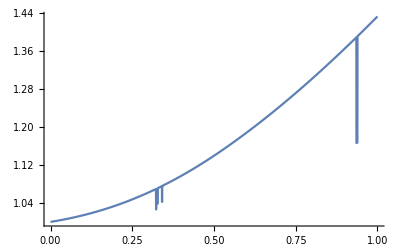

```mathematica
Plot[getMax3[{1,x,0}][[1]],{x,0,1}]
```

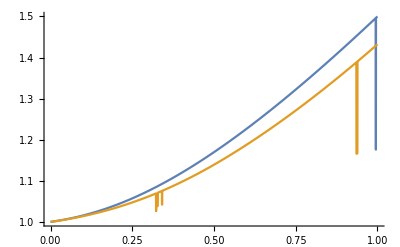

```mathematica
(*compare the order 2 and order 3, seems order 2 actually gives higher value always and therefor tighter bound so order 3 adds nothing *)
Plot[{getMax2[{1,x,0}][[1]],getMax3[{1,x,0}][[1]]},{x,0,1}]
```